```mathematica
V0=1;
Tmax=0.1;
DiamP=8;
Nmax=128;
E0=0;
```

```mathematica
FV[j_,n_,V0_]:=V0*Sqrt[2*Pi]*Sum[(DiscreteDelta[k-j]-DiscreteDelta[k+j])/2/I/k,{k,1,n}];
A[n_]:=Table[Sum[1/k,{k,1,m}],{m,1,n}];
P[n_]:=Table[1/k/A[n][[n]],{k,1,n}]/2;
(* n = 4 *)
Print["kappa = ",kappa=A[4][[4]]];
m2=2*Sum[P[4][[k]]*k^2,{k,1,Length[P[4]]}];
R[t_]=4*Sqrt[m2*kappa*t];
RC=R[Tmax];
h=(RC+DiamP)/Nmax;
E0Shift=IntegerPart[E0*Tmax/h];
```

kappa = 25/12

```mathematica
Stream=OpenRead["~/MSU/matrix/re"];
Mat=Read[Stream];
Close[Stream];
```

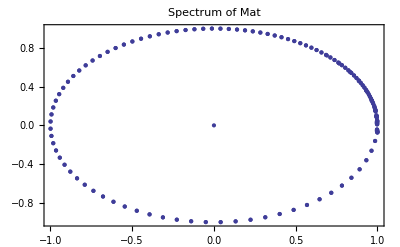

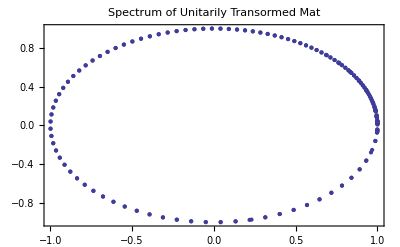

```mathematica
(* Спектр Mat должен лежать вблизи единчной окружности *)
Ed=IdentityMatrix[Length[Mat]];

EigM=Eigenvalues[Mat];
SpM=Table[{Re[EigM[[k]]],Im[EigM[[k]]]},{k,1,Length[Mat]}];

SpecM=ListPlot[SpM,Frame->True,PlotLabel->"Spectrum of Mat",
    PlotRange->All]
    
    (* Унитаризация разрешающего опратора и оценка спектра *)
CMat=Conjugate[Transpose[Mat]];
EU=Inverse[Ed+Mat];
EUC=Inverse[Ed+CMat];
H=0.5*I*((Ed-Mat).EU-(Ed-CMat).EUC);
U=(Ed+I*H).Inverse[Ed-I*H];
EigU=Eigenvalues[U];

SpU=Table[{Re[EigU[[k]]],Im[EigU[[k]]]},{k,1,Length[U]}];

SpecU=ListPlot[SpU,Frame->True,
      PlotLabel->"Spectrum of Unitarily Transormed Mat",
      PlotRange->All]
```

# Отбор для Mat по мининуму L_ 2 нормы производной - РАБОТАЕТ, НО НЕ ОЧЕНЬ!

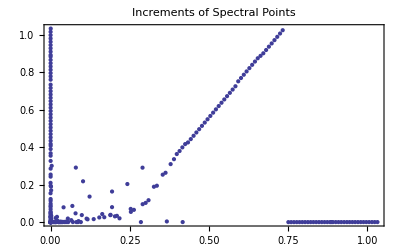

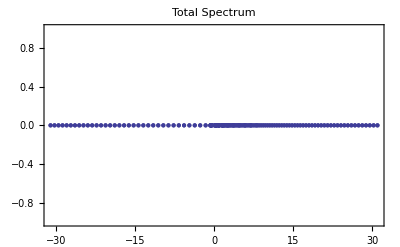

```mathematica
(* Факторизация собстевенных значений  mod(2 * Pi * E0) *)      
EngEv=Arg[EigM]/Tmax;
SE=Sort[EngEv];
DSE=Table[SE[[k+1]]-SE[[k]],{k,1,Length[SE]-1}];

ListPlot[Table[{DSE[[k]],Sort[DSE][[k]]},{k,1,Length[DSE]}],Frame->True,PlotLabel->"Increments of Spectral Points",PlotRange->All]

(*EV=Select[EngEv,And[#>=-kappa,#<=kappa]&]
If[EV=={},Print["No approximate ground eigenvalue has been found!"]]
Spectrum=Table[{EV[[k]],0},{k,1,Length[EV]}]; *)

(*  L - Факторизация спектра для Mat. *)
(*Print["Expected period of the spectrum  L = 2*Pi*E0 =",L=2*Pi*E0];


Spectrum=Table[{Mod[EngEv[[k]],L],0},{k,1,Length[EngEv]}];
ListPlot[Spectrum,Frame->True,PlotLabel->StyleForm["L-Factorization of the Spectrum"],PlotRange->All,PlotStyle->{RGBColor[0,0,1],PointSize[0.01]}];  *)
    
ListPlot[Table[{Sort[EngEv][[k]],0},{k,1,Length[EngEv]}],Frame->True,PlotLabel->"Total Spectrum",PlotRange->All]
```

```mathematica
(* Вычисление собственных векторов ψ(p) MC -аппроксимации состояний дискретного спектра и их нормировка*)
ESys=Eigensystem[Mat];
State=ESys[[2]];
Print["L_2 норма  MC-аппроксимаций состояний дискретного спектра = ", NormMC=Sqrt[Sum[Abs[State[[1,n]]]^2,{n,1,Length[Mat]}]*h]];
```

L_2 норма  MC-аппроксимаций состояний дискретного спектра = 0.306186

Сортированные L_2-нормы производной модуля MC -аппроксимаций состояний дискретного спектра и их номера

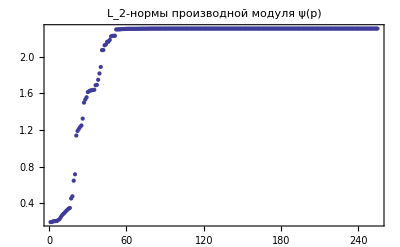

{2,5,4,3,1,20,6,232,108,251,194,209,249,69,254,253,252,225,250,185,212,219,220,215,193,222,214,218,224,8,211,255,238,226,227,105,221,223,216,9,10,95,50,133,208,210,7,38,217,203,29,205,139,202,145,207,34,171,164,229,200,204,198,199,148,191,142,206,201,248,236,237,157,113,109,186,11,213,121,147,187,197,124,166,195,179,174,102,17,21,150,152,60,56,84,41,52,183,159,188,35,196,235,189,154,126,162,43,13,12,163,233,37,48,16,231,18,155,182,181,180,151,128,144,167,172,177,130,156,175,141,173,137,134,169,153,115,118,127,165,123,160,158,120,245,112,149,110,146,106,103,143,138,100,242,136,97,94,132,91,129,31,88,122,125,85,119,81,116,77,114,74,111,70,49,107,58,66,89,54,45,104,62,101,92,99,96,234,42,86,28,25,39,82,24,64,36,78,32,75,71,65,15,22,61,33,57,80,53,30,140,131,23,26,76,117,72,135,67,63,14,19,59,55,192,51,190,46,27,47,184,44,40,98,178,93,176,90,87,170,83,168,79,73,161,68,247,228,244,246,230,243,239,241,240}

{0.19421,0.196293,0.20194,0.2054,0.205587,0.206714,0.217674,0.227695,0.249736,0.270439,0.284966,0.298035,0.314042,0.327841,0.341169,0.349155,0.452529,0.476423,0.646881,0.716828,1.1406,1.19099,1.21276,1.23449,1.25051,1.32563,1.50051,1.53422,1.55864,1.61554,1.62589,1.63299,1.63488,1.63825,1.64034,1.69028,1.69418,1.7495,1.81873,1.88973,2.07402,2.07503,2.12682,2.1363,2.16548,2.16564,2.18452,2.22388,2.22891,2.23021,2.23067,2.29939,2.30017,2.30066,2.30129,2.30312,2.30383,2.30429,2.30572,2.30627,2.3066,2.30685,2.30686,2.30687,2.30691,2.30704,2.30705,2.30708,2.30711,2.30792,2.30792,2.30796,2.30819,2.30822,2.30824,2.30833,2.30858,2.30884,2.3089,2.30898}

```mathematica
Print["Сортированные L_2-нормы :043f:0440:043e:0438:0437:0432:043e:0434:043d:043e:0439 модуля MC -аппроксимаций состояний дискретного спектра и их номера "]; 

NormDMC=Table[Sqrt[Sum[(Abs[State[[k,n-1]]]-Abs[State[[k,n+1]]])^2,{n,2,Length[Mat]-1}]],{k,1,Length[Mat]}]/NormMC/2;

ListPlot[SN=Sort[NormDMC],PlotRange->All,PlotLabel->StyleForm["L_2-нормы :043f:0440:043e:0438:0437:0432:043e:0434:043d:043e:0439 модуля ψ(p)"],Frame->True]
(* Порядок собственных векторов по убыванию нормы *)
ON=Ordering[NormDMC]
(*Первые 80 L_2-норм  производной модуля ψ(p)*)
Table[SN[[k]],{k,1,80}]
```

```mathematica
(*Интерполяция вещественной и мнимой части, модуля и аргумента *)
PsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Re[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

IPsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Im[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

APsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Abs[State[[k,n]]]/NormMC},{n,1,Length[Mat]}]];

FPsiMC[k_]:=Interpolation[Table[{(n+1)*h-DiamP-RC, Arg[State[[k,n]]]},{n,1,Length[Mat]}]];

XPsi[k_,x_]:=Sum[State[[k,n]]*Exp[I*((n+1)*h-DiamP-RC)*x],{n,1,Length[Mat]}]*h/Sqrt[2*Pi];
```

k = 2; λ = -0.700441

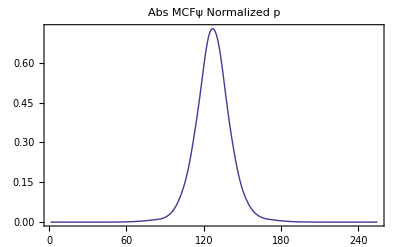

k = 4; λ = -0.637428

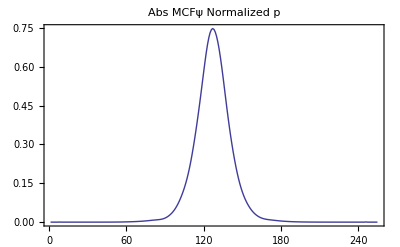

k = 251; λ = -0.450844

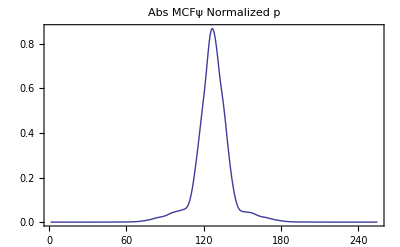

Null^2

```mathematica
(* Ручной выбор вариантов среди кандидатов в списке норм первой производной и интерполяция графика *)
cand={1,3,10};
Do[{
Print["k = ",j=ON[[cand[[k]]]],"; λ = ",EngEv[[j]]];
Print[ListPlot[Abs[State[[j]]]/NormMC,Frame->True,PlotRange->All,PlotLabel->Normalized Abs MCFψ(p), PlotJoined->True]];
(*Print["|ψ(x)| in X-representation at x0 = ",x0=(Arg[State[[j,127]]]-Arg[State[[j,128]]])/h];
Print[Plot[Abs[XPsi[j,x]],{x,x0-10,x0+10},PlotRange->All,Frame->True]];*)
},
{k,1,Length[cand]}]
```

Num of Ev = 249;   λ = -0.41728

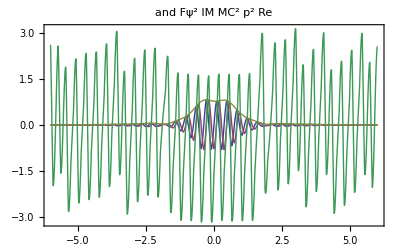

Num of Ev = 108;   λ = -0.465729

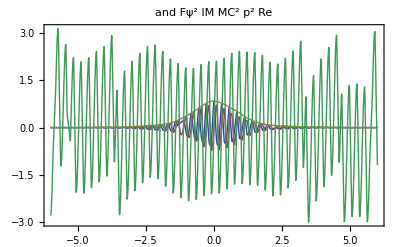

Num of Ev = 1;   λ = -0.732743

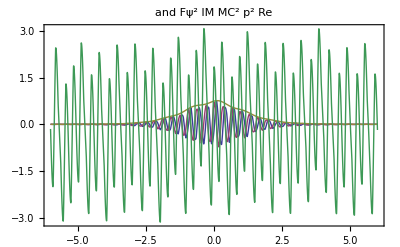

```mathematica
Needs["PlotLegends`"]
Do[{
Print[" Num of Ev = ",cj=ON⟦cand⟦j⟧⟧,";   λ = ",EngEv⟦cj⟧],
Print[Plot[
{PsiMC[cj][p],IPsiMC[cj][p],APsiMC[cj][p],FPsiMC[cj][p]},
{p,-6,6},
Frame->True,PlotRange->All,PlotLabel->Re MC Fψ(p) and  IM MC Fψ(p),PlotLegend->{"Re MCFφ[p]","Im MCFφ[p]","Abs MCFφ[p]","Arg MCFφ[p]"}]
]},
{j,1,Length[cand]}]
```

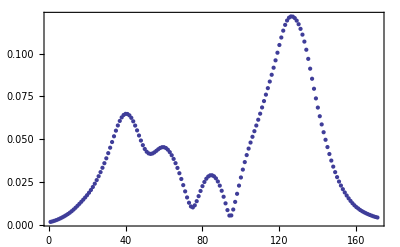

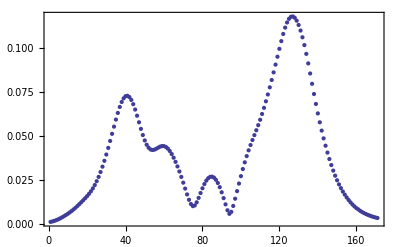

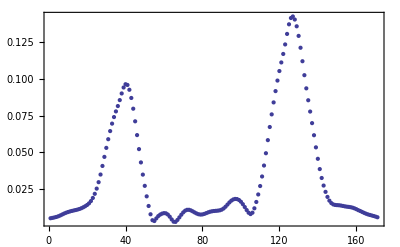

```mathematica
(* Оценка погрешности вычислений в уравнении (H - λ)Fψ = 0 для решений из списка cand *)
(*Оценка погрешности для решения,построенного по матрице Mat*)
err[k_]:=Table[(((n+1)*h-DiamP-RC)^2/2-EngEv[[k]])*State[[k,n]]-I*E0*(State[[k,n+1]]-State[[k,n-1]])/2/h-
1/Sqrt[2*Pi]*Sum[Sum[If[Abs[j*h-i]<h/2,FV[i,4,V0],0],{i,-4,4}]*State[[k,-j+n]],{j,-IntegerPart[RC/h],IntegerPart[RC/h]}], {n,IntegerPart[RC/h]+1,Length[Mat]-IntegerPart[RC/h]}]/NormMC;

Do[
k=ON[[cand[[j]]]];
Print[ListPlot[Abs[err[k]],Frame->True,PlotRange->All]];
, {j,1,Length[cand]}];
```

# Отбор для Mat по инимальной дисперсии | p | - РАБОТАЕТ!

```mathematica
Print["Сортирвка дисперсии модуля MC -аппроксимаций состояний дискретного спектра и их номера "]; 

MeanP=Table[Sum[Abs[State[[k,n]]]^2*(n*h-DiamP-RC),{n,1,Length[U]}],{k,1,Length[U]}]/NormMC;
DispP=Table[Sum[Abs[State[[k,n]]]^2*(n*h-DiamP-RC-MeanP[[k]])^2,{n,1,Length[U]}],{k,1,Length[U]}]/NormMC;
SN=Sort[DispP]
ON=Ordering[DispP]
```

Сортирвка дисперсии модуля MC -аппроксимаций состояний дискретного спектра и их номера

{1.10633,1.32974,1.41025,1.78161,1.79346,2.05628,2.08635,2.21947,2.25173,2.30316,2.3168,2.90528,2.9293,3.31591,3.6104,3.73188,3.81041,3.82052,3.98131,4.00925,4.37202,4.70005,4.84242,4.92906,5.01419,5.07409,5.47584,6.82672,7.0506,7.09585,7.23343,7.3163,7.40773,7.41971,7.56983,8.04029,8.14212,12.3137,12.9529,13.125,13.6228,14.2563,14.2808,20.4869,20.823,21.0144,21.7787,29.8946,30.2926,30.297,39.4007,41.2794,42.8716,44.6741,49.2019,52.9735,53.1129,59.3563,69.8088,69.8216,77.4984,82.4775,85.0997,91.2035,98.8724,110.641,114.36,119.96,125.242,127.208,128.404,137.168,145.462,146.499,157.816,161.787,168.021,177.508,178.372,188.312,199.268,211.066,222.662,233.78,234.303,245.275,245.929,258.218,270.661,271.238,284.132,296.955,297.311,310.449,310.779,324.227,338.293,338.576,352.931,367.288,367.565,382.237,382.49,396.264,397.467,408.995,412.988,428.178,429.021,440.961,444.133,445.117,461.306,461.505,477.996,478.187,488.897,494.98,512.244,512.432,522.761,529.994,533.962,547.69,547.85,551.298,565.846,566.,584.262,584.296,603.011,603.18,621.956,622.211,641.406,641.536,661.031,661.156,680.949,681.069,701.161,701.27,721.61,721.778,742.462,742.574,763.563,763.664,784.951,785.049,795.667,806.631,806.724,816.979,828.699,850.877,850.967,873.445,873.528,896.305,896.385,906.748,919.459,919.535,942.98,966.622,966.72,990.687,990.754,1015.02,1015.08,1039.64,1039.83,1044.25,1063.87,1064.57,1089.78,1115.06,1115.29,1140.86,1141.09,1166.96,1167.18,1193.35,1193.57,1220.26,1247.,1247.23,1274.27,1274.51,1280.58,1301.82,1302.07,1329.65,1330.15,1358.04,1368.23,1386.49,1414.44,1415.23,1443.38,1444.27,1472.51,1473.61,1500.21,1503.24,1533.16,1561.12,1563.38,1590.51,1593.89,1617.97,1622.7,1624.7,1631.5,1656.06,1687.08,1691.23,1718.77,1739.36,1750.76,1771.25,1783.04,1792.23,1815.61,1843.05,1848.48,1881.65,1887.75,1894.03,1907.96,1915.11,1929.03,1948.86,1952.05,1957.69,1982.96,1983.11,2016.48,2050.78,2050.93,2051.12,2086.03,2121.29,2156.77,2156.81,2192.63,2201.57,2228.75,2265.16,2290.9,2301.71,2338.85,2346.83,2377.27}

{249,251,108,232,6,4,20,2,5,1,3,254,252,253,250,209,194,225,69,185,219,211,215,212,214,193,218,223,224,8,222,221,220,105,216,9,10,7,133,203,217,95,50,34,205,210,208,11,213,38,29,191,142,199,148,196,126,207,202,204,206,200,172,201,164,187,139,195,128,166,198,174,171,186,183,145,188,159,189,162,163,182,181,155,180,179,154,151,150,177,175,144,173,141,169,137,134,167,165,130,160,127,158,156,123,153,120,118,149,115,124,146,112,143,110,138,136,106,103,132,100,129,56,97,125,19,94,122,119,91,88,116,85,114,81,111,77,107,74,104,70,101,66,99,62,96,58,92,54,89,121,49,86,45,82,42,78,39,75,36,71,28,32,65,61,25,57,22,53,18,48,16,84,37,41,80,76,33,72,30,67,26,63,23,59,55,15,51,14,46,31,13,43,12,102,98,52,93,47,90,44,87,40,83,35,79,73,27,68,24,64,21,152,60,17,197,192,147,190,140,184,135,178,131,176,231,170,168,117,237,229,161,113,157,109,235,236,248,247,233,234,246,245,244,230,243,242,228,241,240,227,239,238,226,255}

k = 249; λ = -0.41728

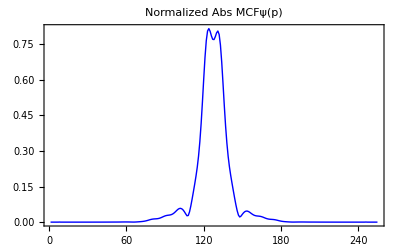

k = 108; λ = -0.465729

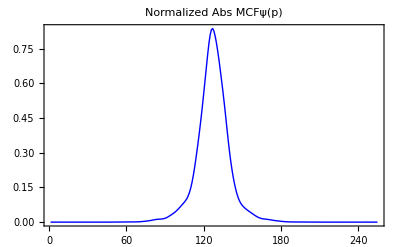

k = 1; λ = -0.732743

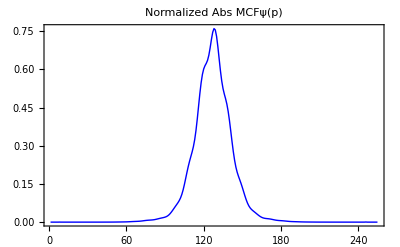

```mathematica
(* Ручной выбор вариантов среди кандидатов в списке дисперсии и интерполяция графика *)
cand={1,3,10}; 
Do[{
Print["k = ",j=ON[[cand[[k]]]],"; λ = ",EngEv[[j]](*, ";  λ(mod L) = ",Mod[EngEv[[j]],L]*)];
Print[ListPlot[Abs[State[[j]]]/NormMC,
Frame->True,PlotRange->All, PlotLabel->"Normalized  Abs MCFψ(p)",PlotJoined->True,PlotStyle->{RGBColor[0,0,1]}]];
(*
Print["|ψ(x)| in X-representation at x0 = ",x0=(Arg[State[[j,127]]]-Arg[State[[j,128]]])/h];
Print[Plot[Abs[XPsi[j,x]],{x,x0-10,x0+10},PlotRange->All,Frame->True]]
*)
(*;
Print["Arg[ψ(x)] in X-representation at x0 = ",x0];
Plot[Arg[XPsi[j,x]],{x,x0-6,x0+6},PlotRange->All,Frame->True]*)
},
{k,1,Length[cand]}];
   
(*Do[{Print["k = ",ON[[cand[[k]]]],"; λ = ",EngEv[[ON[[cand[[k]]]]]], ";  λ(mod L) = ",Mod[EngEv[[ON[[cand[[k]]]]]],L]];ListPlot[Arg[State[[ON[[cand[[k]]]]]]],Frame->True,PlotRange->All, PlotLabel->StyleForm[" Arg MCFψ(p)"],
      DefaultFont->{"Courier",14},
   PlotStyle->{RGBColor[1,0,0]}]},{k,1,Length[cand]}];   *)
```

k = 249;    λ = -0.41728

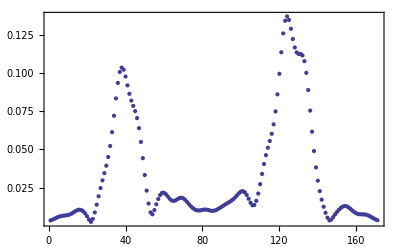

k = 108;    λ = -0.465729

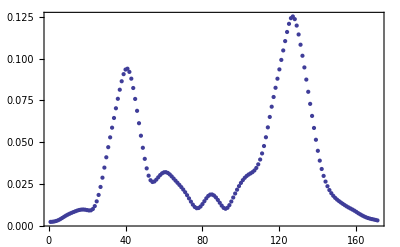

k = 1;    λ = -0.732743

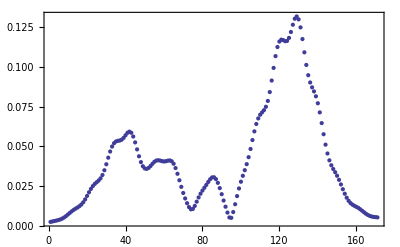

```mathematica
(* Оценка погрешности для решения, построенного отбором по дисперсии для  матрицы Mat *)
err[k_]:=Table[(((n+1)*h-DiamP-RC)^2/2-EngEv[[k]])*State[[k,n]]-I*E0*(State[[k,n+1]]-State[[k,n-1]])/2/h-
1/Sqrt[2*Pi]*Sum[Sum[If[Abs[j*h-i]<h/2,FV[i,4,V0],0],{i,-4,4}]*State[[k,-j+n]],{j,-IntegerPart[RC/h],IntegerPart[RC/h]}], {n,IntegerPart[RC/h]+1,Length[Mat]-IntegerPart[RC/h]}]/NormMC;

Do[{
k=ON[[cand[[j]]]];
Print["k = ",k,";    λ = ",EngEv[[k]](*, ";  λ(mod L) = ",Mod[EngEv[[k]],L]*)];Print[ListPlot[Abs[err[k]],Frame->True,PlotRange->All]]},
{j,1,Length[cand]}
]
```